```mathematica
Clear["Global`*"];
Remove["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Import Files

```mathematica
readMatlabComplex[file_]:=ToExpression[StringSplit[StringReplace[ReadList[file,"String"],{"e"->"*10^","i"->"*I"}],","]]
```

```mathematica
allFiles=FileNames["*.csv"];
allData=readMatlabComplex[#]&/@allFiles;
```

ToExpression::sntx: Invalid syntax in or before "sampl*Ing rat*10^: 78.125 MHz".
                                                                   ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator crossov*10^r 174.6 kHz".
                                                  ^

ToExpression::sntx: Invalid syntax in or before "*Int*10^grator saturat*Ion +43.0 dB".
                                                  ^

General::stop: Further output of ToExpression::sntx
     will be suppressed during this calculation.

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi
     will be suppressed during this calculation.

```mathematica
numoffiles=Dimensions[allFiles][[1]];
index=Table[i,{i,1,numoffiles}];
fileswithindex=Thread[{index,allFiles}];
dataset=Table[allData[[i]][[19;;]],{i,1,numoffiles}];
numset=Table[Dimensions[dataset[[i]]][[1]],{i,1,numoffiles}];
fileswithindex
```

{{1,100100P_20230417_201152_HighResData.csv},{2,100100X_20230417_201126_HighResData.csv},{3,LPam0pm_10_20230412_214245_HighResData.csv},{4,LPam_10pm0_20230412_213845_HighResData.csv},{5,Lpamoffpmoff_20230412_212225_HighResData.csv},{6,LXam0pm_10_20230412_214340_HighResData.csv},{7,LXam_10pm0_20230412_213812_HighResData.csv},{8,LXamoffpmoff_20230412_212345_HighResData.csv},{9,offoffP2_20230417_201024_HighResData.csv},{10,offoffX2_20230417_201057_HighResData.csv}}

## Density matrix in Fock basis

```mathematica
bin=320; (*Dimension of Discretized quadrature value Better be even?*)
n=8;  (*Photon number cutoff*)
dim=n+1; (*Dimension of density matrix*)

(*Ensuring positive semidefiniteness, trace property*)
rr=LowerTriangularize[Array[Subscript[r,##]&,{dim,dim}]];
ii=LowerTriangularize[Array[Subscript[im,##]&,{dim,dim}]];
ii=ii-DiagonalMatrix[Diagonal[ii]];
ii=ⅈ*ii;
t=rr+ii;
(*Density Matrix*)
ρ= ConjugateTranspose[t] . t/Tr[ConjugateTranspose[t] . t] ;
```

## Fock State Wave Function

```mathematica
fn=16;(*Pre-caculation*) 
psi[m_,x_]=HermiteH[m,x]/(√(2^m m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
Tpsi=Table[psi[m,x],{m,0,fn}];
```

## Shot Noise Unit Estimation

```mathematica
size1=Dimensions[allData[[9]][[19;;]]];
size1=size1[[1]];
vacp=Table[allData[[9]][[19;;]][[i]][[2]],{i,1,size1}];
snu1=StandardDeviation[vacp]
mp=Mean[vacp]

size2=Dimensions[allData[[10]][[19;;]]];
size2=size2[[1]];
vacx=Table[allData[[10]][[19;;]][[i]][[2]],{i,1,size2}];
snu2=StandardDeviation[vacx]
mx=Mean[vacx]
(*Shot noise unit is manually fit to match vacuum data with our theoretical expectation*)
(*1.43 magic number*)
snu=(snu1+snu2);
```

4.86853×10^-6

-0.0000116228

4.88555×10^-6

-0.0000116536

## Discretizing Phase Space of the Signal

```mathematica
(*slice=snu*n/(bin/2);
event1=ConstantArray[0,bin+1];
event3=ConstantArray[0,bin+1];
(*63*)
(*X-Quadrature of the Data*)
xsize=Dimensions[allData[[6]][[19;;]]];
xsize=xsize[[1]];
xquad=Table[allData[[6]][[19;;]][[i]][[2]],{i,1,xsize}];

(*P-Quadrature of the Data*)
psize=Dimensions[allData[[3]][[19;;]]];
psize=psize[[1]];
pquad=Table[allData[[3]][[19;;]][[i]][[2]],{i,1,psize}];*)
```

## Squeezed vacuum generation

```mathematica
slice=snu*n/(bin/2);
(*hbar=1*)
(*squeezing parameter *)
r=0.5;
(*Rotation parameter θ*)
ang=3*Pi/4;



funcx=Integrate[1/Pi*Exp[-((x*Cos[ang]-p*Sin[ang])^2)/Exp[-1]-
((x*Sin[ang]+p*Cos[ang])^2)/Exp[1]],{p,-Infinity,Infinity}];
plus1[x_]=funcx//N

func2=Integrate[1/Pi*Exp[-((x*Cos[ang
+Pi/4]-p*Sin[ang+Pi/4])^2)/Exp[-1]-
((x*Sin[ang+Pi/4]+p*Cos[ang+Pi/4])^2)/Exp[1]],{p,-Infinity,Infinity}];
plus2[x_]=func2//N

funcp=
Integrate[1/Pi*Exp[-((x*Cos[ang]-p*Sin[ang])^2)/Exp[-1]-
((x*Sin[ang]+p*Cos[ang])^2)/Exp[1]],{x,-Infinity,Infinity}];
plus3[p_]=funcp//N

func4=Integrate[1/Pi*Exp[-((x*Cos[ang
+Pi/4]-p*Sin[ang+Pi/4])^2)/Exp[-1]-
((x*Sin[ang+Pi/4]+p*Cos[ang+Pi/4])^2)/Exp[1]],{x,-Infinity,Infinity}];
plus4[p_]=func4//N
```

0.275476 2.71828^(0.5-0.648054 x^2)

0.56419 2.71828^(0.5-2.71828 x^2)

0.275476 2.71828^(0.5-0.648054 p^2)

0.56419 2.71828^(-0.5-0.367879 p^2)

## Squeezed vacuum Event

```mathematica
(*epsilon to avoid zero in the denominator*)
ϵ=0.00000000001;
event1=Table[(plus1[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm1=Sum[event1[[i]],{i,1,bin+1}];
norm1//N
event1=event1/norm1;

event2=Table[(plus2[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm2=Sum[event2[[i]],{i,1,bin+1}];
norm2//N
event2=event2/norm2;

event3=Table[(plus3[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm3=Sum[event3[[i]],{i,1,bin+1}];
norm3//N
event3=event3/norm3;

event4=Table[(plus4[(i-bin/2)/((bin)/2)*n+ϵ]),{i,0,bin}];
norm4=Sum[event4[[i]],{i,1,bin+1}];
norm4//N
event4=event4/norm4;
```

20.

20.

20.

«1 more identical outputs»

## Counting Events

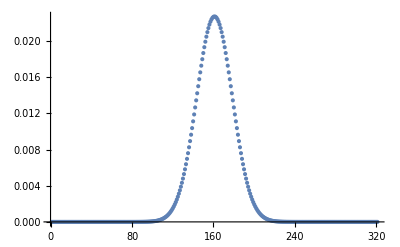

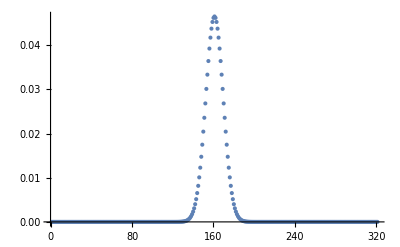

-Graphics-

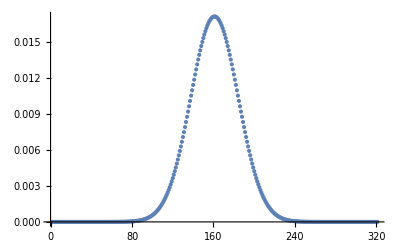

```mathematica
(*(*Counting Occurence*)
For[i=1,i<xsize+1,i++,
event1[[Round[(xquad[[i]]-mx)/slice]+bin/2]]=event1[[Round[(xquad[[i]]-mx)/slice]+bin/2]]+1;]

For[i=1,i<psize+1,i++,
event3[[Round[(pquad[[i]]-mp)/slice]+bin/2]]=event3[[Round[(pquad[[i]]-mp)/slice]+bin/2]]+1;]

(*Normalization*)
event1=event1/xsize;
event3=event3/psize;*)

(*Gmn is imported, discretized and normalized occurence of event*)
G={event1,event2,event3,event4}//N;
ListPlot[event1, PlotRange->Full]
ListPlot[event2, PlotRange->Full]
ListPlot[event3,PlotRange->Full]
ListPlot[event4, PlotRange->Full]
```

## Normalization Parameter for Projector

```mathematica
hermite0=Table[(psi[0,(i-bin/2)/(bin/2)*n])^2,{i,0,bin}];
norm=Sum[hermite0[[i]],{i,1,bin+1}];
norm//N
hermite0=hermite0/norm;
```

20.

## Projector Represented in quadrature basis

```mathematica
(*Matrix Element in Fock basis*)
Π=Table[(Tpsi[[a+1]]Tpsi[[b+1]]/norm)ⅇ^(ⅈ(b-a)θ),{a,0,n},{b,0,n}] ;
```

## Discretize X and θ

```mathematica
theta={0,Pi/4,Pi/2,3*Pi/4};
quad=Subdivide[-n,n,bin];
```

## Deviation Function

```mathematica
Q=Re[
Sum[(      G[[j,i]]-(  Tr[Π.ρ]/.{x->quad[[i]],θ->theta[[j]]}  )   )^2,{i,1,bin+1},{j,1,4}]
];
```

## Optimization Kernel

```mathematica
flat1=DeleteCases[Flatten[rr],_Integer];
flat2=DeleteCases[Flatten[-ⅈ*ii],_Integer];
kernel=Join[flat1,flat2];
```

## Maximum Entropy reconstruction

```mathematica
solution=FindMinimum[Q,kernel];

Chop[ρ /. solution[[2]] ];

Chop[MatrixForm[ρ /. solution[[2]]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(0.882082 | -0.0000501504-0.000141763 ⅈ | -0.000848183-0.285101 ⅈ | 0.000386878-0.000389211 ⅈ | -0.116329-0.00207717 ⅈ | 0.000453484+0.000396477 ⅈ | -0.0000778877+0.0567935 ⅈ | 0.000177329+0.000588045 ⅈ | 0.022331-0.00747938 ⅈ
-0.0000501504+0.000141763 ⅈ | 0.0000316155 | 0.0000599968+0.0000199081 ⅈ | -2.35646×10^-6-4.43091×10^-6 ⅈ | -0.000145035+0.0000193748 ⅈ | 8.40797×10^-6-2.45149×10^-6 ⅈ | 0.000130376+0.0000855294 ⅈ | 3.53169×10^-6+8.57696×10^-7 ⅈ | 0.0000662834-0.000084291 ⅈ
-0.000848183+0.285101 ⅈ | 0.0000599968-0.0000199081 ⅈ | 0.0925132 | 0.000132612+0.000132488 ⅈ | 0.000537651-0.0378326 ⅈ | -0.000137787+0.000145869 ⅈ | -0.018254+8.72262×10^-6 ⅈ | -0.000193698+0.0000623699 ⅈ | 0.00237948+0.00730446 ⅈ
0.000386878+0.000389211 ⅈ | -2.35646×10^-6+4.43091×10^-6 ⅈ | 0.000132612-0.000132488 ⅈ | 7.71794×10^-6 | -0.0000885955-0.0000975238 ⅈ | -5.94431×10^-6-4.64582×10^-7 ⅈ | -0.0000608274+0.0000225582 ⅈ | -9.77522×10^-7+1.31389×10^-6 ⅈ | 4.35656×10^-6+0.000047583 ⅈ
-0.116329+0.00207717 ⅈ | -0.000145035-0.0000193748 ⅈ | 0.000537651+0.0378326 ⅈ | -0.0000885955+0.0000975238 ⅈ | 0.018185 | -0.0000691873-0.0000643074 ⅈ | -0.000449268-0.00862144 ⅈ | -0.0000334328-0.000088058 ⅈ | -0.00335366+0.00133347 ⅈ
0.000453484-0.000396477 ⅈ | 8.40797×10^-6+2.45149×10^-6 ⅈ | -0.000137787-0.000145869 ⅈ | -5.94431×10^-6+4.64582×10^-7 ⅈ | -0.0000691873+0.0000643074 ⅈ | 0.0000133031 | 0.0000561712+0.000076956 ⅈ | 3.05591×10^-6+6.74914×10^-7 ⅈ | 0.0000771775-0.0000670554 ⅈ
-0.0000778877-0.0567935 ⅈ | 0.000130376-0.0000855294 ⅈ | -0.018254-8.72262×10^-6 ⅈ | -0.0000608274-0.0000225582 ⅈ | -0.000449268+0.00862144 ⅈ | 0.0000561712-0.000076956 ⅈ | 0.00551829 | 0.0000583675-0.000014738 ⅈ | -0.000600922-0.00223564 ⅈ
0.000177329-0.000588045 ⅈ | 3.53169×10^-6-8.57696×10^-7 ⅈ | -0.000193698-0.0000623699 ⅈ | -9.77522×10^-7-1.31389×10^-6 ⅈ | -0.0000334328+0.000088058 ⅈ | 3.05591×10^-6-6.74914×10^-7 ⅈ | 0.0000583675+0.000014738 ⅈ | 1.95792×10^-6 | 0.000024716-0.0000390993 ⅈ
0.022331+0.00747938 ⅈ | 0.0000662834+0.000084291 ⅈ | 0.00237948-0.00730446 ⅈ | 4.35656×10^-6-0.000047583 ⅈ | -0.00335366-0.00133347 ⅈ | 0.0000771775+0.0000670554 ⅈ | -0.000600922+0.00223564 ⅈ | 0.000024716+0.0000390993 ⅈ | 0.00164699)

## Plotting Real part of Density Matrix

```mathematica
DiscretePlot3D[Abs@Re[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Plotting Imaginary part

```mathematica
DiscretePlot3D[Abs@Im[ρ /. solution[[2]]][[i+1, j+1]], {i, 0, n}, {j, 0, n}, 
 ExtentSize -> Full]
```

-Graphics3D-

## Wigner Reconstruction

```mathematica
g=2;
M=n+1;
xrange={-5,5};
yrange={-5,5};
linespace=100;
rho=ρ /. solution[[2]];
%//MatrixForm;
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]}
{xx,yy}=meshgrid[Array[#&,linespace,xrange],Array[#&,linespace,yrange]];
aa=0.5*g*(xx+ⅈ yy);
%//MatrixForm;
wlist=Table[Table[Table[0,{i,1,M}],{j,1,M}],{k,1,M}];
wlist[[1]]=Exp[-2 Abs[aa]^2]/π;
W=Re[rho[[1,1]]]*Re[wlist[[1]]];

For[nn=1, nn<M,nn++,
wlist[[nn+1]]=(2.0*aa*wlist[[nn]])/√nn;
W+=2*Re[rho[[1,nn+1]]*wlist[[nn+1]]];
]


For[mm=1, mm<M,mm++,

temp=wlist[[mm+1]];
wlist[[mm+1]]=(2*Conjugate[aa]*temp-√mm*wlist[[mm]])/√mm;
W+=Re[rho[[mm+1,mm+1]]*wlist[[mm+1]]];
For[nn=mm+1, nn<M,nn++,
temp2=(2*aa*wlist[[nn]]-√mm*temp)/√nn;
temp=wlist[[nn+1]];
wlist[[nn+1]]=temp2;
W+=2*Re[rho[[mm+1,nn+1]]*wlist[[nn+1]]];
]
]
list=0.5*W*g^2;
pos=Position[list,_?(#==Max[list]&)]
Min[list]
disp=Sqrt[((50-pos[[1,1]])/10)^2+((50-pos[[1,2]])/10)^2]//N
ListPlot3D[0.5*W*g^2,PlotRange->All, Boxed->False,DataRange->{{-5,5},{-5,5}}]
```

{{51,51}}

-0.00833599

0.141421

-Graphics3D-